## Solving Multiple Rigid Pendulums

7/16/2020 Joshua Cheung

In this notebook, we simulate the motion of multiple, connected pendulum where the masses are connected by rigid strings. Note that by choosing specific values for the masses and lengths of the pendulums, our program will simulate a single pendulum where the connecting string also has mass.

### Define constants

```mathematica
n =10;            (* Number of pendulums *)
g = 9.81;     (* Gravitational constant, in m/sec/sec *)
tfinal = 20;  (* Final time for the numerical solution *)

mass = 1;     (* Mass of pendulum in kg *)
mList = Table[mass, n];
mList[[n]] = 2;           (* Use this line to simulate a string with mass *)

length = 1;(* Length of a singular pendulumm, in m *)
lList=Table[length, n];
```

Initial Conditions

```mathematica
θ0 =π/8;   (* Initial angle of all pendulums *)
θ0List = Table[θ0,n];

ω0 = 0;         (* Initial angular velocity *)
ω0List=Table[ω0,n];
```

### Determine Governing Equations

First let’s define the θ’s and our x and y positions in time. Note that x and y are functions of θ in the mathematical sense.

```mathematica
θList[t_] = Table[θ[i][t], {i,n}];
x[t_] ={ lList[[1]] *Sin[θ[1][t]]};
Do[x[t_]=Append[x[t], x[t][[i-1]]+lList[[i]]*Sin[θ[i][t]]], {i, 2, n}]
y[t_] = {- lList[[1]]*Cos[θ[1][t]]};
Do[y[t_]=Append[y[t], y[t][[i-1]] - lList[[i]]*Cos[θ[i][t]]], {i,2,n}]
```

Now let’s define the Lagrangian of our system: 	L = kinetic energy - potential energy

```mathematica
PE = Sum[mList[[i]]*g*y[t][[i]],{i,n}];
KE = Simplify[Sum[1/2 mList[[i]]((x'[t][[i]])^2+(y'[t][[i]])^2),{i,n}]];
L = KE - PE;
```

Now, let’s define our system of governing equations using the Euler-Lagrange differential equation
d/dt((δ L)/(δ θ')) - (δ L)/(δ θ) 	for every θ

```mathematica
eqns[t_]={};
Do[eqns[t_]=Append[eqns[t],{D[D[L,θ[i]'[t]],t]-D[L,θ[i][t]] == 0}],{i,n}]
eqns[t_] = Flatten[eqns[t]];
```

Now let’s add our initial conditions to our system of equations.

```mathematica
Do[eqns[t_]=Append[eqns[t],{θ[i][0]==θ0List[[i]], θ[i]'[0]==ω0List[[i]]}],{i,n}]
eqns[t_]=Flatten[eqns[t]];
```

### Numerically Solve ODE

```mathematica
θSols = θList[t] /.  NDSolve[eqns[t],θList[t], {t, 0, tfinal},Method-> {"EquationSimplification"->"Residual"}][[1]];
```

### Visualize Our Results

Plotting our results can be useful as a quick sanity check.

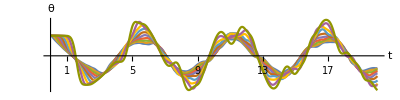

```mathematica
Plot[θSols, {t,0,tfinal}, PlotRange-> All, PlotStyle->Rainbow,AspectRatio->1/4, Ticks->{Range[tfinal],{-π,0,π,3π,5π,7π}}, AxesLabel->{"t","θ"}, PlotLegends->{"1", "2", "3", "4","5", "6","7", "8", "9", "10"}  ]
```

Now let’s make an animation of the solution. We should note that Mathematica’s Graphics function uses a different coordinate system than we have been using so far. To avoid this problem let’s define our solution functions in Cartesian coordinates. To do this we will essentially repeat the same process as before but now with our solution θ’s.

```mathematica
xPos[t_] = {lList[[1]]*Sin[θSols[[1]]]};
Do[xPos[t_] = Append[xPos[t], xPos[t][[i-1]]+lList[[i]]*Sin[θSols[[i]]]], {i,2,n}]
yPos[t_] = {-lList[[1]]*Cos[θSols[[1]]]};
Do[yPos[t_] = Append[yPos[t], yPos[t][[i-1]]-lList[[i]]*Cos[θSols[[i]]]],{i,2,n}]
```

Now let’s make a list of all of our shapes to display.

```mathematica
lines[t_] = {Line[{{0,0},{xPos[t][[1]], yPos[t][[1]]}}]};
Do[lines[t_]=Append[lines[t], Line[{{xPos[t][[i-1]], yPos[t][[i-1]]},{xPos[t][[i]], yPos[t][[i]]}}]],{i,2,n}]
```

```mathematica
massScale = (.2)/Max[mList];
disks[t_] = {{Blue, Disk[{xPos[t][[1]], yPos[t][[1]]}, massScale*mList[[1]]]}};
Do[disks[t_]= Append[disks[t],{Blue, Disk[{xPos[t][[i]], yPos[t][[i]]}, massScale*mList[[i]]]}], {i,2,n}]
```

```mathematica
shapes[t_] = Append[lines[t], disks[t]];
```

Finally, we can create the animation. Note that the bobs are sized proportionally to the largest mass.

```mathematica
totalLength = Total[lList] + 1;
Animate[Graphics[shapes[t], PlotRange->{{-totalLength, totalLength},{-totalLength-2, 5}}], {t,0,tfinal}, DefaultDuration-> tfinal]
```